```mathematica
(* MA39110 / Assignment 7 / 16MA20053 / NER ROHIT *)
ClearAll["Global`*"];
```

```mathematica
Thomas[a_,b_,c_,d_]:=Module[{c1=Range[Length[c]],d1=Range[Length[d]],x=Range[Length[b]]},
c1[[1]]=c[[1]]/b[[1]]; d1[[1]]=d[[1]]/b[[1]];
Do[
If[i≠Length[d],c1[[i]]=c[[i]]/(b[[i]]-a[[i-1]]*c1[[i-1]])];
d1[[i]]=(d[[i]]-a[[i-1]]*d1[[i-1]])/(b[[i]]-a[[i-1]]*c1[[i-1]]);
,{i,2,Length[d]}];
x[[Length[b]]]=d1[[Length[b]]];
Do[
x[[i]]=d1[[i]]-c1[[i]]*x[[i+1]];
,{i,Length[b]-1,1,-1}];
x];
Model[n0_,r0_]:=Module[{n=n0,r=r0},
x0=0;xf=1;h=(xf-x0)/n;
A=Table[0,{x,1,n-1},{y,1,n-1}];
X=Table[x0+x*h,{x,1,n-1}];
XT=Table[x0+x*h,{x,0,n}];
B=Table[0,{x,1,n-1}];
t=100;
PLT=Table[0,{x,1,t}];
y[x_]=Sin[Pi*x];
Y=N[y[XT]];
For[j=1,j<=t,j++,
{
For[i=1,i<n,i++,
{
im=i+1;
A[[i,i]]=-r-1;
B[[i]]=-(r/2)(Y[[im-1]]-2Y[[im]]+Y[[im+1]])-Y[[im]];
If[i≠1,A[[i,i-1]]=r/2];
If[i≠n-1,A[[i,i+1]]=r/2];
}];
Y=N[Flatten[{{y[0]},Thomas[Diagonal[A,-1],Diagonal[A],Diagonal[A,1],B],{y[1]}}]];
PLT[[j]]=ListLinePlot[Transpose[{XT,Y}]];
};];
Show[PLT[[1;;;;5]],PlotLabel->Style[StringForm["h = ``, r = ``",h,r]]]
];
```

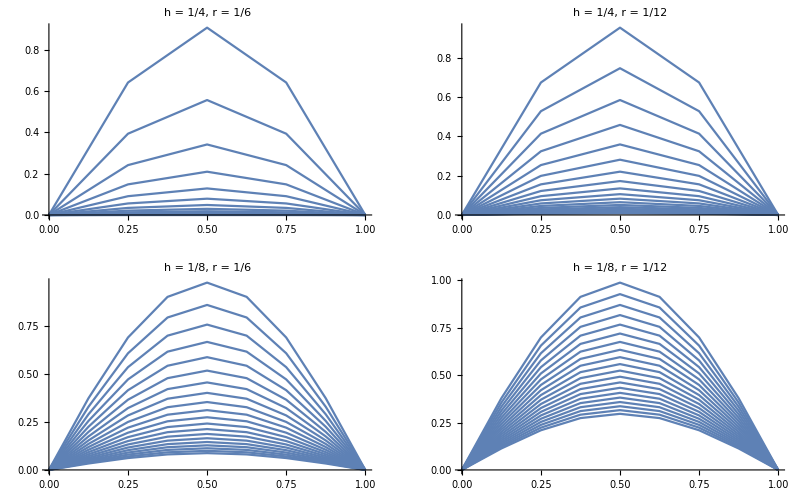

```mathematica
p1=Model[4,1/6];
p2=Model[8,1/6];
p3=Model[8,1/12];
p4=Model[4,1/12];
Rotate[GraphicsGrid[{{p1,p4},{p2,p3}}],Pi/2]
```

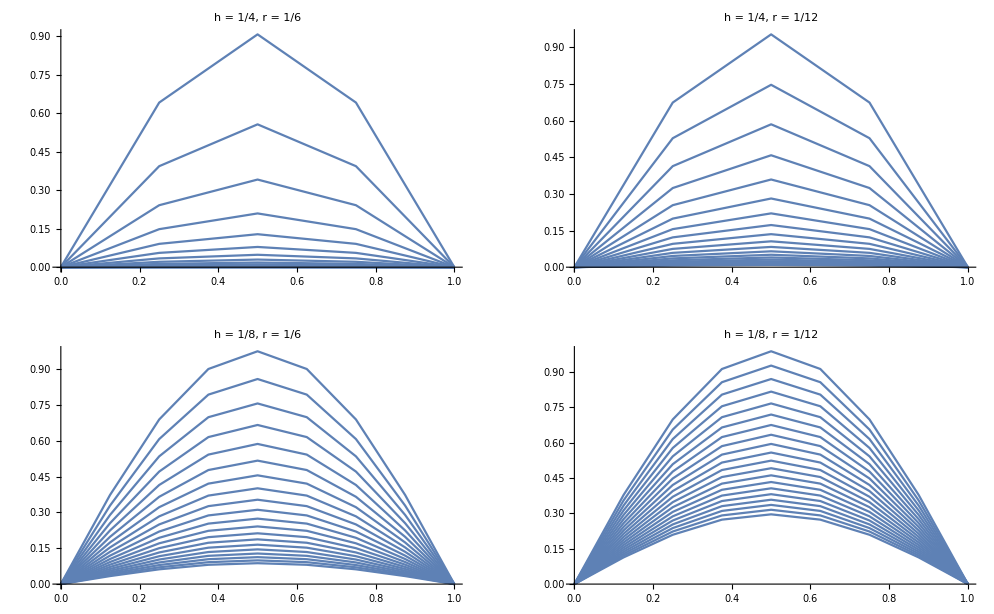

-Graphics-